# Pertołów

## Dane

### Nazwy plików konfiguracyjnych

```mathematica
(*fileg="configgLG"; 
*)
```

### Tensor metryczny

```mathematica
(*{g,x}=ReadList[fileg]*)
```

```mathematica
(* kowariantny tensor metryczny gμν - NALEŻY USTAWIĆ!; uwaga! numeracja w tabeli jest od 1 *)
(* wymiar przestrzeni: namx = liczba wierszy = liczba kolumn w tensorze metrycznym *)
nmax=4; 

(* longitudinal gauge, brak przestrzennych elementów pozadiagonalnych w tensorze energii-pędu, czas kosmiczny, zerowa krzywizna *)
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];
(* tensor metryczny bez perturbacji *)
(*g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];*)

(* czy zmienne Mukhanova-Sasakiego stosować *)
mMS=True;
(*mMS=False;*)
(* lista zmiennych, w których zapisana jest metryka - NALEŻY USTAWIĆ! *)
x={t,x1,x2,x3};
```

### Lagranżjan

```mathematica
(* liczba pól skalarnych N - NALEŻY USTAWIĆ! *)
lpol=3;

(* pomocniczy wektor z polami skalarnymi ϕ^I *)
(* nazwy pól - MOŻNA USTAWIĆ! (domyślnie ϕ1,ϕ2,...) *)
(*pola=Table[ToExpression["ϕ"<>ToString[I]],{I,1,lpol}]; *)
pola={ϕ,χ,ψ};

(* metryka G w przestrzeni pól (tablica współczynników przy wyrazach z pochodnymi pól w lagranżjanie - zależą od pól) - więc tablica jest symetryczna *)
(* pola bez argumentów - NALEŻY USTAWIĆ! *)
(*fG=Table[If[I<=J,ToExpression["G"<>ToString[I]<>ToString[J]],ToExpression["G"<>ToString[J]<>ToString[I]]][Sequence@@pola],{I ,1,lpol } ,{J ,1,lpol }];*) 
fG=Table[Which[ I == J , 1, True , 0 ],{I ,1,lpol} ,{J ,1,lpol}];

(* lagranżjan z artykułu arXiv:1401.6163v3 L=P(X,pola) *)
(* pola bez argumentów i ogólnie zapisany człon kinetyczny XK, jeżeli potencjał jest wpisywany ogólnie to wstawiamy V[Sequence@@pola] - NALEŻY USTAWIĆ! *)
(*La=fP[XK,Sequence@@pola]; *)
La=XK-V[Sequence@@pola];

(* funkcje i parametry, występujące w lagranżjanie - NALEŻY USTAWIĆ! *)
fun={V->(3*Subscript[H, 0]^2+(-Sqrt[2*(1/10^2)]*3*Subscript[H, 0]^2)*({#1,#2,#3}.{Cos[Subscript[Θ, max]*(1+Tanh[s*#1])/2],Sin[Subscript[Θ, max]*(1+Tanh[s*#1])/2],0})+(1/2)100*Subscript[H, 0]^2*({#1,#2,#3}.{-Cos[Subscript[Φ, max]*(1+Tanh[s*#1])/2]Sin[Subscript[Θ, max]*(1+Tanh[s*#1])/2],Cos[Subscript[Φ, max]*(1+Tanh[s*#1])/2]Cos[Subscript[Θ, max]*(1+Tanh[s*#1])/2],-Sin[Subscript[Φ, max]*(1+Tanh[s*#1])/2]})^2 &)};
(*param=Rationalize[{Subscript[H, 0]->10^(-4),s->200,Subscript[Φ, max]->Pi/8,Subscript[Θ, max]->Pi/6}];*)
param=Rationalize[{Subscript[H, 0]->1,s->200,Subscript[Φ, max]->Pi/8,Subscript[Θ, max]->Pi/6}];

(* grawitacyjna część lagranżjanu w teorii f(R) (domyślnie f(R)=R), skalar Ricciego musi być oznaczony przez rr[Sequence@@pola] - NALEŻY USTAWIĆ *)
fR=rr[Sequence@@x];

(* nazwa tworzonego pliku z równaniami - NALEŻY USTAWIĆ! *)
sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\potencjalKT\\3polaKT\\__nowe__";
nazwaplikurow="3polaKT";
```

```mathematica
(* potencjał *)
VT[x1_,x2_,x3_]:=V[x1,x2,x3] /.fun /. param
Plot3D[Evaluate[VT[xx,yy,0]],{xx,-3.,3.},{yy,-3.,3.},AxesLabel->{"ϕ","χ","V"},ColorFunction->Function[{x,y,z},Hue[z]],PlotRange->All,Filling->Bottom,Axes->{True,True,True}]
```

-Graphics3D-

## Program

```mathematica
(* wyłączenie komunikatów o użyciu funkcji Inverse przez Solve *)
Off[Solve::ifun];
(* wyłączenie komunikatów o rozwiązywaniu równań algebraicznych i różniczkowych *)
Off[NDSolve::pdord];
```

```mathematica
Needs["mrkFasadaPertolow`"]
```

### Równania

```mathematica
(* tensor metryczny w longitudinal gauge *)
Block[{Lag,potencjal,Masa,ruchurow0,polarow000,ruchurow1,polarow001,polarow011,rowMS1,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* gęstość lagranżjanu *)
Lag=Expand[ℒ==Lagrangian[g,x,pola,fG,La,0]];
(* potencjał *)
potencjal=V[Sequence@@pola]==(V[Sequence@@pola] /. fun) ;
(* macierz masy *)
Masa=MacierzMasy[g,x,pola,fG,La,False];
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=RuchuRownaniakw[g,x,pola,fG,La,1];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* równania dla zmiennych Mukhanova-Sasakiego *)
rowMS1=If[mMS,MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1],False];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La,False];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,mMS,1,True],600,{}];
(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,mMS,1,True];
(* zapisanie wyników do notebooka *)
wpisNb={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Macierz masy",Masa},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"F",sciezka];
wpisB={"Macierz masy",Masa};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"M",sciezka];
)]//AbsoluteTiming
```

10:47:36GMT+2.TimeObject[{10,47,36.3991},TimeZone→2.] Równania ruchu w rzędzie 0

10:47:37GMT+2.TimeObject[{10,47,37.2742},TimeZone→2.] Równania ruchu w rzędzie 0

10:47:37GMT+2.TimeObject[{10,47,37.6862},TimeZone→2.] Równania ruchu w rzędzie 0

10:47:38GMT+2.TimeObject[{10,47,38.0925},TimeZone→2.] Równanie pola 00 w rzędzie 0

10:47:38GMT+2.TimeObject[{10,47,38.1237},TimeZone→2.] Równania ruchu w rzędzie 1

10:47:38GMT+2.TimeObject[{10,47,38.5124},TimeZone→2.] Równania ruchu w rzędzie 1

10:47:38GMT+2.TimeObject[{10,47,38.825},TimeZone→2.] Równania ruchu w rzędzie 1

10:47:39GMT+2.TimeObject[{10,47,39.0906},TimeZone→2.] Równanie pola 00 w rzędzie 1

10:47:39GMT+2.TimeObject[{10,47,39.325},TimeZone→2.] Równanie pola 01 w rzędzie 1

10:47:39GMT+2.TimeObject[{10,47,39.4968},TimeZone→2.] Równanie pola 11 w rzędzie 0

10:47:39GMT+2.TimeObject[{10,47,39.5593},TimeZone→2.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

10:47:42GMT+2.TimeObject[{10,47,42.0073},TimeZone→2.] Baza Freneta

10:47:47GMT+2.TimeObject[{10,47,47.0902},TimeZone→2.] Baza Freneta

10:47:47GMT+2.TimeObject[{10,47,47.2934},TimeZone→2.] Pochodne potencjału w zmiennych σ i s

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

10:50:50GMT+2.TimeObject[{10,50,50.1051},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

10:57:49GMT+2.TimeObject[{10,57,49.9326},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

11:07:48GMT+2.TimeObject[{11,7,48.2315},TimeZone→2.] Równania ruchu dla zmiennych współporuszających się

Drop::drop: Cannot drop positions -1 through -1 in {}.

{1213.43,Null}

### Wartości początkowe

```mathematica
Print[TimeObject[Now]];
{tloi,Ntot, tfTot}=Block[{wstepneWP,wstepneWSP,Nall},(
(* szukanie wartości początkowych *)
(* całkowita liczba e-powiększeń - NALEŻY USTAWIĆ! *)
Nall=72;
(* wstępne wartości początkowe i współczynniki - NALEŻY USTAWIĆ! *)
wstepneWP={-4.84,0.1,0.}; 
wstepneWSP={0.,0.,0.};
WartosciPoczatkoweTlo[pola,fG,La,g,x,fR,Nall,wstepneWP,wstepneWSP,fun,param])]
```

15:32:18GMT+2.TimeObject[{15,32,18.9189},TimeZone→2.]

15:32:19GMT+2.TimeObject[{15,32,19.0751},TimeZone→2.] Równanie pola 00 w rzędzie 0

15:32:19GMT+2.TimeObject[{15,32,19.2158},TimeZone→2.] Równanie pola 11 w rzędzie 0

15:32:19GMT+2.TimeObject[{15,32,19.372},TimeZone→2.] Równania ruchu w rzędzie 0

15:32:20GMT+2.TimeObject[{15,32,20.5439},TimeZone→2.] Równania ruchu w rzędzie 0

15:32:20GMT+2.TimeObject[{15,32,20.9814},TimeZone→2.] Równania ruchu w rzędzie 0

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ϕ[0.]==-4.84,χ[0.]==0.1,ψ[0.]==0.,ϕ'[0.]==0.103943,χ'[0.]==-2.44996,ψ'[0.]==0.,nn[0.]==0.}

71.982

{{{-57697296142578112/11920928955078125,5960464477539062/59604644775390625,0},{6195477182035389/59604644775390625,-29205759520691648/11920928955078125,0}},858091936718715392/11920928955078125,4392422026036671488/59604644775390625}

```mathematica
{tloi,Ntot, tfTot}={{{-57697296142578112/11920928955078125,5960464477539062/59604644775390625,0},{6195477182035389/59604644775390625,-29205759520691648/11920928955078125,0}},858091936718715392/11920928955078125,4392422026036671488/59604644775390625};
```

```mathematica
%//N
```

{{{-4.84,0.1,0.},{0.103943,-2.44996,0.}},71.982,73.6926}

```mathematica
(* końcowy czas *)
tf=tfTot;
```

```mathematica
(* początkowa wartość liczby e-powiększeń dla tła (N0t) i perturbacji (N0p) - NALEŻY USTAWIĆ! *)
N0t=-12.;
N0p=N0t;
N0p=-8.;
```

### Tło

```mathematica
Test 
(* czas kosmiczny dla danej liczby e-powiększeń *)
Block[{testN},(
testN={30,31,32,33,34,35};
testN={32.2,32.3};
CzasN[testN,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{37.6681044604275102003219,37.7660345739680933937363}

```mathematica
(* zakresy i czasy wykorzystywane przy rysowaniu wykresów - NALEŻY USTAWIĆ! *)
{p30,p31,p32,p322,p323,p33,p34,p35}={35.5355655,36.499803880,37.47250952675, 37.6681044604275, 37.766034573968,38.454073025381,39.444907054736,40.4452769082};

tzakresBazaM={{p30},{p322}};
tzakresBazaF={p30,p322};
tzakresB={p32,p33};
tB=p33;
(*tN0=pm0;

lista500zc=Join[Range[m01,m002,100],Range[m002,p002,16],Range[p002,p015,77],{tf}];(*{81,250,169}*)
gridzc={{},{m002,pm0,p002,p015},{m01,p015},{m01,p015},{m01,p015}};

lista500={{tf},lista500zc};*)
```

```mathematica
(* efektywna prędkość dźwięku *)
PredkoscDzwiekuEf[g,x,pola,fG,La]
```

1

```mathematica
(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
Block[{zakres={},lista=lista500},
(*lista=Join[listazc,{lista1000[[2]]}];*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p01},Table[p01,Length[lista]-1]]};
(*zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};*)
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres];]//AbsoluteTiming
```

{652.589,Null}

```mathematica
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->{{0},{tf}}];//AbsoluteTiming
```

16:51:15GMT+2.TimeObject[{16,51,15.1583},TimeZone→2.] Równanie pola 00 w rzędzie 0

16:51:15GMT+2.TimeObject[{16,51,15.4083},TimeZone→2.] Równania ruchu w rzędzie 0

16:51:16GMT+2.TimeObject[{16,51,16.4865},TimeZone→2.] Równania ruchu w rzędzie 0

16:51:16GMT+2.TimeObject[{16,51,16.8771},TimeZone→2.] Równania ruchu w rzędzie 0

16:51:19GMT+2.TimeObject[{16,51,19.1896},TimeZone→2.] Czasy

16:51:19GMT+2.TimeObject[{16,51,19.9553},TimeZone→2.] Epilog

16:51:19GMT+2.TimeObject[{16,51,19.9553},TimeZone→2.] Wykres 1

16:51:20GMT+2.TimeObject[{16,51,20.4709},TimeZone→2.] Wykres 2

16:51:20GMT+2.TimeObject[{16,51,20.6896},TimeZone→2.] Wykres 3

16:51:20GMT+2.TimeObject[{16,51,20.9084},TimeZone→2.] Wykres 3D

{7.10936,Null}

```mathematica
(*(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]]+0.2*wartpocz[[2,3]],fun,param,sciezka];//AbsoluteTiming*)
```

```mathematica
(* pochodne pól w zależności od liczby e-powiększeń *)
PochodnePol[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

16:11:41GMT+2.TimeObject[{16,11,41.7209},TimeZone→2.] Liczba e-powiększeń

16:11:41GMT+2.TimeObject[{16,11,41.7209},TimeZone→2.] Wykres 1

16:11:41GMT+2.TimeObject[{16,11,41.9396},TimeZone→2.] Wykres 2

16:11:42GMT+2.TimeObject[{16,11,42.1584},TimeZone→2.] Wykres 3

16:11:42GMT+2.TimeObject[{16,11,42.3459},TimeZone→2.] Wykres energii kinetycznej

{1.01416,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy Freneta, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,zakrest->tzakresBazaF];//AbsoluteTiming
```

16:54:41GMT+2.TimeObject[{16,54,41.35},TimeZone→2.] Prędkości kątowe bazy

16:54:41GMT+2.TimeObject[{16,54,41.4282},TimeZone→2.] Liczba e-powiększeń i zmienne

16:54:41GMT+2.TimeObject[{16,54,41.4282},TimeZone→2.] Wykres

{41.6777,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->tzakresBazaM, gridt->{}];//AbsoluteTiming
```

16:55:26GMT+2.TimeObject[{16,55,26.9698},TimeZone→2.] Wykres prędkości kątowych bazy

{14.5275,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń
z uwzględnieniem produkcji cząstek *)
Block[{grid={{},{}},zakres,lista=lista500},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p015},Table[p015,Length[lista]-1]]};
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres,gridt->grid];]//AbsoluteTiming
```

{679.435,Null}

```mathematica
(* kwadraty mas w zależności od liczby e-powiększeń *)
Block[{opisy={}},
(*opisy={Superscript["m","2"],Superscript["M","2"]};*)
Masy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t, legenda->opisy];]//AbsoluteTiming
```

16:56:29GMT+2.TimeObject[{16,56,29.0818},TimeZone→2.] Liczba e-powiększeń i masy

16:56:29GMT+2.TimeObject[{16,56,29.0818},TimeZone→2.] Wykres

{4.66383,Null}

```mathematica
(* kwadraty efektywnych mas w zależności od liczby e-powiększeń (po przejściu do bazy Freneta dla zakrzywionych trajektorii) *)
MasyEfektywne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

21:40:25GMT+2.TimeObject[{21,40,25.5458},TimeZone→2.] Macierz masy w bazie Freneta

21:40:25GMT+2.TimeObject[{21,40,25.5458},TimeZone→2.] Prędkości kątowe bazy

21:40:25GMT+2.TimeObject[{21,40,25.5614},TimeZone→2.] Efektywna macierz masy

21:40:26GMT+2.TimeObject[{21,40,26.1083},TimeZone→2.] Liczba e-powiększeń i masy

21:40:26GMT+2.TimeObject[{21,40,26.1083},TimeZone→2.] Wykres

{547.059,Null}

```mathematica
Test 
(* wartości bazy wektorów własnych macierzy masy dla pierwotnych pól i bazy Freneta w danej chwili t *)
Block[{testt,bm,bf},(testt=0;
bm=SetPrecision[BazaMasyTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
Print["BM: ",bm];
bf=SetPrecision[BazaFrenetaTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
 Print["BF: ",bf];)]
```

Test

BM: {{-0.99996,0.0088865,-3.0513×10^-840},{0.0088865,0.99996,-3.4335×10^-838},{0,-3.4336×10^-838,-1.}}

BF: {{0.042388,-0.9991,0},{0.9991,0.042388,4.0361×10^-825},{-4.0325×10^-825,-1.7108×10^-826,1.}}

k_turn: 0.00001 ; k(N=3.)=0.000201: {0.000294,0.00287,0.0162}

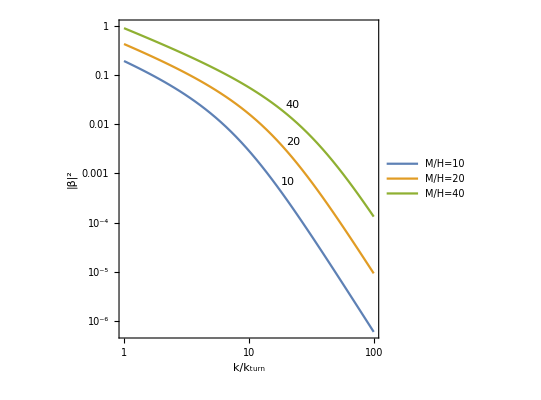

```mathematica
(* liczba obsadzeń w uproszczonej wersji *)
Block[{ml={Subscript[m, ϕ]},mh={M}, kwT,kw, Nkw, r,lo,oznaczenia,legenda},(Nkw=3.;
ml={10^(-7),10^(-7),10^(-7)};mh={10^(-4),2*10^(-4),4*10^(-4)};

{kwT,kw}=Take[WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],2];

r=MapThread[Sqrt[(kw^2+#2^2)/(kw^2+#1^2)] &,{ml,mh}];
Print["k_turn: ",SetPrecision[kwT,3]," ; k(N=",Nkw,")=",SetPrecision[kw,3],": ",SetPrecision[(((Sqrt[r]-1/Sqrt[r])Sin[Δθ])^2)/4 /. param,3]];
lo=Function[{k,ml,mh},(((Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]]-1/Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]])Sin[Δθ])^2)/4 /. param];

oznaczenia={10,20,40};
legenda=Map["StyleBox[\"M\",\nFontSlant->\"Italic\"]/StyleBox[\"H\",\nFontSlant->\"Italic\"]="<>ToString[#] &,oznaczenia];
LogLogPlot[Evaluate[MapThread[Labeled[lo[k*kwT,ml[[#1]],mh[[#1]]],#2,{Scaled[0.5],Above}] &, {Range[Length[oznaczenia]],oznaczenia}]],{k,1,1*10^2},Frame->True, AspectRatio->1, FrameLabel->{"StyleBox[\"k\",\nFontSlant->\"Italic\"]/SubscriptBox[ StyleBox[\"k\",\nFontSlant->\"Italic\"], \"turn\"]","|β|^2"},PlotLegends->Placed[legenda,{Left,Bottom}]]
)]
```

```mathematica
(* gęstość energii wyprodukowanych ciężkich cząstek w uproszczonej wersji *)
Block[{mh},(mh={10^(-4), 2*10^(-4), 4*10^(-4), 5*10^(-4), 10^(-3),1.5*10^(-3),1.65*10^(-3),1.7*10^(-3),1.8*10^(-3),1.9*10^(-3), 2*10^(-3)};
Print["l ", N[mh^4*Sin[Δθ]^2/(24*Pi^2) /. param]];
Print["h ", N[mh^4*Sin[Δθ]^2/(16*Pi^2) /. param]];)]
```

l {4.03138×10^-20,6.45021×10^-19,1.03203×10^-17,2.51961×10^-17,4.03138×10^-16,2.04089×10^-15,2.98806×10^-15,3.36705×10^-15,4.23198×10^-15,5.25373×10^-15,6.45021×10^-15}

h {6.04707×10^-20,9.67531×10^-19,1.54805×10^-17,3.77942×10^-17,6.04707×10^-16,3.06133×10^-15,4.48209×10^-15,5.05057×10^-15,6.34797×10^-15,7.8806×10^-15,9.67531×10^-15}

```mathematica
(* wykresy elementów bazy wektorów własnych macierzy masy *)
WykresyBazaMasy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

16:57:34GMT+2.TimeObject[{16,57,34.3133},TimeZone→2.] Liczba e-powiększeń i baza wektorów własnych macierzy masy

16:57:34GMT+2.TimeObject[{16,57,34.3133},TimeZone→2.] Wykres wierszy 1

16:57:50GMT+2.TimeObject[{16,57,50.5286},TimeZone→2.] Wykres wierszy 2

16:57:50GMT+2.TimeObject[{16,57,50.8255},TimeZone→2.] Wykres wierszy 3

16:57:51GMT+2.TimeObject[{16,57,51.0755},TimeZone→2.] Wykres kolumn 1

16:57:51GMT+2.TimeObject[{16,57,51.3567},TimeZone→2.] Wykres kolumn 2

16:57:51GMT+2.TimeObject[{16,57,51.638},TimeZone→2.] Wykres kolumn 3

{17.6381,Null}

```mathematica
(* wykresy elementów bazy Freneta *)
WykresyBaza[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

16:57:55GMT+2.TimeObject[{16,57,55.2474},TimeZone→2.] Liczba e-powiększeń i baza

16:57:55GMT+2.TimeObject[{16,57,55.2474},TimeZone→2.] Wykres wierszy 1

16:58:37GMT+2.TimeObject[{16,58,37.7391},TimeZone→2.] Wykres wierszy 2

16:58:38GMT+2.TimeObject[{16,58,38.7078},TimeZone→2.] Wykres wierszy 3

16:58:39GMT+2.TimeObject[{16,58,39.0203},TimeZone→2.] Wykres kolumn 1

16:58:39GMT+2.TimeObject[{16,58,39.3016},TimeZone→2.] Wykres kolumn 2

16:58:39GMT+2.TimeObject[{16,58,39.6297},TimeZone→2.] Wykres kolumn 3

{44.7104,Null}

```mathematica
Test 
(* wykresy funkcji zależnych od pól i liczby e-powiększeń oraz ich pierwszych pochodnych w zależności od liczby e-powiększeń *)
Block[{funkcje,opisy,
Lao},(
(*funkcje={Map[#'[x[[1]]]/Symbol["nn"]'[x[[1]]] &, pola]};
opisy={{"wkladPM",Map[ToString[#]<>"'(t)/H" &, pola]}};*)

funkcje={Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,False]] // Flatten};
opisy={{"C","coefficients",{"C_σs1","C_s1σ"}}};

(*funkcje={{Symbol["nn"]'[x[[1]]]}};
opisy={{"H",{"H"}}};*)

(*Lao=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{4}][[1]]/. Symbol["P"]->0;*)

(*funkcje={{Abs[Symbol["τ"][x[[1]]]]}};
opisy={{"tau",{"tau"}}};*)

WykresyTestoweTlo[funkcje,opisy,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];)]//AbsoluteTiming
```

Test

04:24:26GMT+2.TimeObject[{4,24,26.5446},TimeZone→2.] Liczba e-powiększeń

04:24:26GMT+2.TimeObject[{4,24,26.5602},TimeZone→2.] Wykres 1

{7.7539,Null}

### Perturbacje

```mathematica
(* widma *)
(* widma w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

18:33:56GMT+2.TimeObject[{18,33,56.4979},TimeZone→2.]

18:33:56GMT+2.TimeObject[{18,33,56.7167},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny (O)

```mathematica
(* perturbacje w zależności od liczby e-powiększeń *)
PerturbacjeB[pola,fG,La,g,x,fR,tloi,lista500zc,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"wsp",5.5},NkwNorm->0.,norm->"",tftot->tfTot,baza->"",RS->False,pertu->False];//AbsoluteTiming
```

04:42:48GMT+2.TimeObject[{4,42,48.5409},TimeZone→2.] Liczba e-powiększeń i widma

kw 0.0000549728

tf A {28.4502,4.50617}

tf {Re,Im} {{{27.4032,7.02014},{4.34746,1.08329}},{{2.9669,0.628479},{0.473532,0.085902}}}

04:42:48GMT+2.TimeObject[{4,42,48.7655},TimeZone→2.] Wykres perturbacji

04:42:59GMT+2.TimeObject[{4,42,59.0633},TimeZone→2.] Wykres wierszy 1

04:43:01GMT+2.TimeObject[{4,43,1.73833},TimeZone→2.] Wykres wierszy 2

04:43:03GMT+2.TimeObject[{4,43,3.93532},TimeZone→2.] Wykres kolumn 1

04:43:05GMT+2.TimeObject[{4,43,5.93501},TimeZone→2.] Wykres kolumn 2

04:43:08GMT+2.TimeObject[{4,43,8.13598},TimeZone→2.] Wykres Re

04:43:14GMT+2.TimeObject[{4,43,14.92},TimeZone→2.] Wykres Im

{452.07,Null}

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Block[{grid={},zakres,lista={{tf}}},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
zakres={Table[0,Length[lista]],Join[{tf},Table[tf,Length[lista]-1]]};
zakres={};
WidmaB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",10},NkwNorm->10.,norm->"h",tftot->tfTot,baza->"M",RS->True,pertu->False,zakrest->zakres,gridt->{}];]//AbsoluteTiming
```

19:05:33GMT+2.TimeObject[{19,5,33.4343},TimeZone→2.]

$Aborted

```mathematica
(* widma w bazie Freneta w zależności od liczby falowej *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

$Aborted

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby falowej *)
Print[TimeObject[Now]];
WidmaB[pola,fG,La,g,x,fR,tloi,{{tf},listatfn1},fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"M",RS->True,pertu->False,zakrest->{{0.,0.},{tf,tf}}];//AbsoluteTiming
```

```mathematica
(* wzmocnienia widma perturbacji krzywizny w zależności od liczby falowej *)
Print[TimeObject[Now]];
Block[{punkty,lista={{tf}}},
punkty=Map[{"wsp", #} &, Join[Range[0.1,3.,0.1],Range[3.,10.,0.1]]];
(*punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];
punkty=Map[{"wsp", #} &, {0.1,1.,2.,10.}];*)
WzmocnienieB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->punkty, NkwNorm->Table[0.,Length[lista]],baza->"M"]]//AbsoluteTiming
```

20:12:21GMT+2.TimeObject[{20,12,21.556},TimeZone→2.]

20:12:21GMT+2.TimeObject[{20,12,21.56},TimeZone→2.]Rozwiązanie 1

20:12:22GMT+2.TimeObject[{20,12,22.9982},TimeZone→2.]Rozwiązanie 2

08:05:11GMT+2.TimeObject[{8,5,11.1045},TimeZone→2.] Wykres widmR(k) - wzmocnienia(k)

{42769.9,Null}

```mathematica
(* punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];
{{tf},listatfn2} *)
{{{0.1,0.9876171190824801},{0.29999999999999993,0.9906318317909778},{0.49999999999999994,1.0016546386896203},{0.6999999999999998,1.0231606669962032},{0.9999999999999999,1.0785430406702896},{1.9999999999999998,1.351131254162129},{2.4999999999999996,1.3966253448609658},{2.9999999999999996,1.3233419976986953},{3.9999999999999996,1.0452929844786882},{4.999999999999999,1.0373814461629576},{5.999999999999999,1.1431897297602687},{7.,1.0564101922980118},{7.999999999999999,1.014035296059254},{8.999999999999998,1.088681236872553},{9.999999999999998,1.0632092895879846}},{{0.1,15.359009033832272},{0.29999999999999993,16.08499229052795},{0.49999999999999994,17.427384209369833},{0.6999999999999998,19.17225868314315},{0.9999999999999999,21.91386132934547},{1.9999999999999998,21.181668163017886},{2.4999999999999996,13.195742276742862},{2.9999999999999996,4.5541499934730245},{3.9999999999999996,1.980341324772158},{4.999999999999999,13.000798306480407},{5.999999999999999,9.753949071942234},{7.,0.5108120350187195},{7.999999999999999,3.5905831293304726},{8.999999999999998,6.168858694727985},{9.999999999999998,1.2903312692047897}}}


(* Pk - 0 *)
{{{0.1,0.9876171190824801},{0.2,0.9885028462134687},{0.3,0.9906318322583718},{0.4,0.9950238043594833},{0.49999999999999994,1.0016546386896203},{0.5999999999999999,1.0109637727047942},{0.7000000000000001,1.0231606095454926},{0.8,1.0383438183769655},{0.8999999999999999,1.057186190275632},{0.9999999999999999,1.0785430406702896},{1.1,1.1027721937432977},{1.2,1.1298077102994348},{1.3,1.1582848201251148},{1.4000000000000001,1.187507327908387},{1.5,1.2177555849710304},{1.6,1.2473171222708808},{1.7,1.276438279380155},{1.8000000000000003,1.304292154673044},{1.9,1.3286676841648801},{1.9999999999999998,1.351131254162129},{2.0999999999999996,1.3690254638880086},{2.2,1.3828569508423834},{2.3,1.3923316939712855},{2.4,1.3971068359472878},{2.5000000000000004,1.3966253434625522},{2.6,1.390716675794293},{2.6999999999999997,1.380723846331224},{2.8000000000000003,1.3653476241455602},{2.9,1.346431032969762},{3.,1.3233419976986953},{3.1,1.297166765898299},{3.2,1.2687833699587407},{3.3,1.2387390910042653},{3.4,1.2077649024275219},{3.5,1.1766753099656495},{3.5999999999999996,1.146262040725412},{3.6999999999999997,1.117269553125542},{3.8,1.0903882640202898},{3.8999999999999995,1.0662322720360065},{3.9999999999999996,1.0452929844786882},{4.1,1.027927037629423},{4.199999999999999,1.0144101911307566},{4.3,1.004910876944129},{4.399999999999999,0.9994291739354728},{4.499999999999999,0.9978600074872325},{4.6,0.9999774847278996},{4.7,1.005451221778378},{4.799999999999999,1.0138517021433193},{4.8999999999999995,1.024683290702745},{4.999999999999999,1.0373814461629576},{5.099999999999999,1.051346160735774},{5.2,1.0659885144148704},{5.299999999999999,1.080646338427171},{5.3999999999999995,1.0948096269204237},{5.5,1.1078830834408286},{5.599999999999999,1.1193794419316774},{5.699999999999999,1.1289633149455565},{5.8,1.1362614211247632},{5.8999999999999995,1.1410264137061967},{5.999999999999999,1.1431897297602687},{6.1,1.1427308168512302},{6.2,1.1396829902225354},{6.299999999999999,1.1342043562136075},{6.4,1.1265653275441438},{6.499999999999999,1.1170970119128933},{6.599999999999999,1.1061693135198227},{6.699999999999999,1.0941907285897057},{6.8,1.0816022158629675},{6.8999999999999995,1.0688591586253688},{7.,1.0564101922980118},{7.099999999999999,1.0446787395971058},{7.199999999999999,1.0340483235808602},{7.299999999999999,1.024850635526138},{7.3999999999999995,1.017355481996348},{7.499999999999999,1.0117630195169545},{7.6,1.0081983769403065},{7.7,1.0067091656433151},{7.799999999999999,1.0072658647387487},{7.9,1.009765048341474},{7.999999999999999,1.014035296059254},{8.099999999999998,1.019845417537366},{8.2,1.0269147206259956},{8.299999999999999,1.0349247776826944},{8.399999999999999,1.0435323080425725},{8.5,1.0523825469693413},{8.6,1.0611226599638357},{8.699999999999998,1.0694144860838317},{8.8,1.0769464984180503},{8.9,1.0834445329367217},{8.999999999999998,1.088681236872553},{9.1,1.09248402748953},{9.2,1.0947408678992525},{9.299999999999999,1.0954029123018107},{9.4,1.094483577832338},{9.5,1.0920545507791526},{9.599999999999998,1.0882406907160498},{9.700000000000001,1.083215430122762},{9.799999999999999,1.0771959663674615},{9.899999999999999,1.0704352603265845},{9.999999999999998,1.0632092895879846}}}


(* Pk - 0, 382 M150*)
{{{0.1,0.9959690448860462},{0.2,0.9979780999366079},{0.30000000000000004,1.0028761784082778},{0.4,1.0115743493819258},{0.5,1.0253408943364732},{0.6,1.044513400321288},{0.7000000000000001,1.0694690244702176},{0.8,1.101058125772909},{0.9,1.1387571320000442},{1.,1.1822018425559888},{1.1,1.231606611944922},{1.2000000000000002,1.284798156703799},{1.3000000000000003,1.3417653420298983},{1.4000000000000001,1.4003875776945856},{1.5000000000000002,1.4606655000921218},{1.6,1.519518645046419},{1.7000000000000002,1.5767360031971729},{1.8000000000000005,1.6307366457701142},{1.9000000000000001,1.679724355823614},{2.,1.7212668696532667},{2.1,1.7566724701888659},{2.2,1.782152275902169},{2.3000000000000003,1.799099344345499},{2.4000000000000004,1.806320355819543},{2.5000000000000004,1.8031188412931574},{2.6,1.789730099982391},{2.7,1.7665563334564351},{2.8000000000000003,1.7341293456578961},{2.9000000000000004,1.693215329421703},{3.0000000000000004,1.6450058812029176},{3.1000000000000005,1.5910376260645773},{3.2,1.5324506707504606},{3.3000000000000003,1.4704344223600556},{3.4000000000000004,1.4072006433368596},{3.5,1.3439483561901182},{3.6,1.282359849583041},{3.7,1.2239504326380963},{3.8000000000000003,1.1700325287835487},{3.9,1.1217797179115419},{4.,1.080251668188302},{4.1,1.0461067560216395},{4.2,1.0199233100814311},{4.3,1.001932679877033},{4.3999999999999995,0.9921197976400604},{4.5,0.9902314402924637},{4.6,0.9957698576358853},{4.7,1.0080223800779047},{4.8,1.026088880929806},{4.9,1.0489208405311858},{5.,1.075361965657902},{5.1,1.104184486045754},{5.2,1.1341292423835108},{5.3,1.1639507561192817},{5.4,1.1924615017851294},{5.5,1.2185712526804415},{5.6,1.2413204594140284},{5.7,1.2599081132236358},{5.8,1.2737135729486533},{5.9,1.2823120903174856},{6.,1.2854831545942516},{6.1,1.2832115992047899},{6.200000000000001,1.2756815778265753},{6.299999999999999,1.2632637206471742},{6.4,1.2464964492295518},{6.500000000000001,1.226061908545652},{6.599999999999999,1.2027573316197568},{6.7,1.1774625349243533},{6.800000000000001,1.1511043523432947},{6.9,1.1246200244075737},{7.,1.0989221488403096},{7.1000000000000005,1.0748675749306429},{7.2,1.053230605015756},{7.300000000000001,1.0346785068464353},{7.4,1.019747960989728},{7.5,1.0088255913590052},{7.6000000000000005,1.002137773345943},{7.7,0.9997500902213281},{7.8,1.0015704935819412},{7.9,1.0073539452731257},{8.,1.0167150683765052},{8.1,1.0291502233774652},{8.2,1.0440581203266583},{8.3,1.0607582797089694},{8.4,1.0785230904625676},{8.5,1.0966160986501317},{8.6,1.1143085791206426},{8.7,1.1308936312955862},{8.8,1.1457335824327788},{8.9,1.1582930324923024},{9.,1.1681212697530674},{9.1,1.1748683742484762},{9.2,1.1783398888859764},{9.3,1.1784736008478491},{9.4,1.1753030610608697},{9.5,1.1690072733338148},{9.6,1.1599006029578438},{9.700000000000001,1.148362146750703},{9.8,1.1348638113047718},{9.9,1.119965794514969},{10.,1.1042394758416543}},{{0.1,7.070268871730846},{0.2,7.176041446387899},{0.30000000000000004,7.349814293319774},{0.4,7.585748541369419},{0.5,7.876099024704283},{0.6,8.210630481072354},{0.7000000000000001,8.577646319721353},{0.8,8.964433741478027},{0.9,9.35645421439698},{1.,9.739222507471977},{1.1,10.098558958242206},{1.2000000000000002,10.419193186309329},{1.3000000000000003,10.68854390472974},{1.4000000000000001,10.893899942313201},{1.5000000000000002,11.025544519619254},{1.6,11.074183897987174},{1.7000000000000002,11.034451648234459},{1.8000000000000005,10.902589132323769},{1.9000000000000001,10.677334330937645},{2.,10.359391972987376},{2.1,9.954487806461213},{2.2,9.467369498801615},{2.3000000000000003,8.908243258690556},{2.4000000000000004,8.287288994589687},{2.5000000000000004,7.616620377976555},{2.6,6.910002269443695},{2.7,6.181944831850602},{2.8000000000000003,5.447271283226459},{2.9000000000000004,4.720750373264094},{3.0000000000000004,4.016804140038406},{3.1000000000000005,3.3490974398055613},{3.2,2.729692931172391},{3.3000000000000003,2.1689435508021915},{3.4000000000000004,1.6759766976525805},{3.5,1.2572131759063527},{3.6,0.9170849785658785},{3.7,0.6577450057464971},{3.8000000000000003,0.4789238886339317},{3.9,0.3781885153188272},{4.,0.35103786189836983},{4.1,0.3909972698164317},{4.2,0.4900696950244024},{4.3,0.6388839084381503},{4.3999999999999995,0.827102809208575},{4.5,1.0437817240402796},{4.6,1.2777277043879003},{4.7,1.517871161527677},{4.8,1.7536176706498539},{4.9,1.9751769499555873},{5.,2.1738517919133447},{5.1,2.342277101261375},{5.2,2.4746086470921465},{5.3,2.5666572431377297},{5.4,2.6159622221113117},{5.5,2.6218019082273893},{5.6,2.5851427813473706},{5.7,2.5085320166497493},{5.8,2.3959387296215833},{5.9,2.2525511861175196},{6.,2.084537927916947},{6.1,1.8987822579362246},{6.200000000000001,1.7026004203736629},{6.299999999999999,1.5034537155700343},{6.4,1.3086652935064187},{6.500000000000001,1.1251514356492454},{6.599999999999999,0.959176392985851},{6.7,0.8161387603481635},{6.800000000000001,0.7003958330683294},{6.9,0.6151315884449705},{7.,0.562272777633523},{7.1000000000000005,0.5424556502820521},{7.2,0.5550428946698915},{7.300000000000001,0.5981869242527349},{7.4,0.6689343479886105},{7.5,0.7633679375880165},{7.6000000000000005,0.8767829661993579},{7.7,1.0038908351562588},{7.8,1.1390379000173452},{7.9,1.2764293102220188},{8.,1.410353911917481},{8.1,1.535403564623071},{8.2,1.6466718873200756},{8.3,1.7399245896624156},{8.4,1.8117473493692957},{8.5,1.8596638615156906},{8.6,1.8822010103836413},{8.7,1.8789103121483552},{8.8,1.850373372947901},{8.9,1.798164442566176},{9.,1.72474276377337},{9.1,1.6333333909915708},{9.2,1.52781457680755},{9.3,1.4125383414208892},{9.4,1.2921235011914811},{9.5,1.1713030827267},{9.6,1.054742563945884},{9.700000000000001,0.946821516127303},{9.8,0.8514941692922372},{9.9,0.7721582597586125},{10.,0.7114983891767995}}}
```

```mathematica
Test 
(* widma dla podanej bazy *)
Print[TimeObject[Now]];
Block[{baza},(
baza={};
baza={{1,0,0},{0,1,0},{0,0,1}};
WidmaTest[baza,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p];)]//AbsoluteTiming
```

16:15:53GMT+2.TimeObject[{16,15,53.1763},TimeZone→2.]

16:15:53GMT+2.TimeObject[{16,15,53.1919},TimeZone→2.] Perturbacje ℛ i 𝒮

16:15:54GMT+2.TimeObject[{16,15,54.8795},TimeZone→2.] Widma

16:15:55GMT+2.TimeObject[{16,15,55.0357},TimeZone→2.] Liczba e-powiększeń i widma

16:15:55GMT+2.TimeObject[{16,15,55.2857},TimeZone→2.] Wykres

{4.00844,Null}

```mathematica
(* korelacje względne *)
Print[TimeObject[Now]];
KorelacjeWzgledne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->{"N",3.}];//AbsoluteTiming
```

01:39:30GMT+2.TimeObject[{1,39,30.8356},TimeZone→2.]

01:39:30GMT+2.TimeObject[{1,39,30.8396},TimeZone→2.] Widma

01:39:30GMT+2.TimeObject[{1,39,30.8714},TimeZone→2.] Korelacje

01:39:30GMT+2.TimeObject[{1,39,30.8724},TimeZone→2.] Korelacje względne

01:39:30GMT+2.TimeObject[{1,39,30.8764},TimeZone→2.] Liczba e-powiększeń i względne korelacje

01:39:30GMT+2.TimeObject[{1,39,30.8784},TimeZone→2.] Wykres

{1.98064,Null}

```mathematica
Print[TimeObject[Now]];
Korelacje[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"h",tftot->tfTot];//AbsoluteTiming
```

01:40:34GMT+2.TimeObject[{1,40,34.8096},TimeZone→2.]

01:40:34GMT+2.TimeObject[{1,40,34.8252},TimeZone→2.] Korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8428},TimeZone→2.] Liczba e-powiększeń i korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8443},TimeZone→2.] Wykres

{1.56311,Null}

```mathematica
Test
(* liczby falowe dla N=0 (k1) i N=Nkw (k2) w momencie przekraczania promienia Hubble'a: k=aH; {k1, k2, k1-k2, k2/k1} *)
Block[{Nkw},(Nkw=3.;
WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{9.99506235933683244134×10^-6,0.000200736634607383730912,-0.000190741572248046898471,20.083580010870738543}

```mathematica
(* liczby obsadzeń *)
(* liczba obsadzeń w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->0.,zakrest->tzakresB];//AbsoluteTiming
```

05:06:21GMT+2.TimeObject[{5,6,21.3583},TimeZone→2.]

05:14:04GMT+2.TimeObject[{5,14,4.10504},TimeZone→2.] Liczba e-powiększeń i liczba obsadzeń

{3.50943×10^-9,1.49779×10^-6}05:14:04GMT+2.TimeObject[{5,14,4.13455},TimeZone→2.]

{1.33444×10^-10,1.99601×10^-10}05:14:04GMT+2.TimeObject[{5,14,4.16809},TimeZone→2.]

{0.00644601,0.00657539}05:14:04GMT+2.TimeObject[{5,14,4.19861},TimeZone→2.]

05:14:04GMT+2.TimeObject[{5,14,4.19911},TimeZone→2.] Wykres

{475.446,Null}

```mathematica
(* liczba obsadzeń w zależności od liczby falowej *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,zakrest->{tB}];//AbsoluteTiming
```

03:26:01GMT+2.TimeObject[{3,26,1.53742},TimeZone→2.]

03:26:01GMT+2.TimeObject[{3,26,1.67498},TimeZone→2.] Liczba obsadzeń

kwNorm: {0.463267,0.829206}03:26:03GMT+2.TimeObject[{3,26,3.71264},TimeZone→2.]

1.5: {1.02366,0.375015}03:26:05GMT+2.TimeObject[{3,26,5.92366},TimeZone→2.]

2: {0.365702,0.228618}03:26:08GMT+2.TimeObject[{3,26,8.31438},TimeZone→2.]

10: {0.0139638,0.0138118}03:26:14GMT+2.TimeObject[{3,26,14.0065},TimeZone→2.]

20: {0.00205275,0.00223467}03:26:23GMT+2.TimeObject[{3,26,23.8839},TimeZone→2.]

03:26:23GMT+2.TimeObject[{3,26,23.8844},TimeZone→2.] Wykres

$Aborted

```mathematica
Test
(* gęstość energii wyprodukowanych na zakręcie cząstek w chwili t0 *)
Print[TimeObject[Now]];
GestoscEnergiiCzastekTest[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS, t0->tN0]//AbsoluteTiming
```

Test

04:56:04GMT+2.TimeObject[{4,56,4.98974},TimeZone→2.]

04:56:13GMT+2.TimeObject[{4,56,13.7468},TimeZone→2.] Gęstości energii wyprodukowanych cząstek

{{0.000099552,0},{0,0.00098715}}

{9.9951×10^-6,{0.00010005,0.0009872}}

4.45893×10^-14

8.78729×10^-14

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny: {kw,kw2,kw-kw2,indeks} *)
Print[TimeObject[Now]];
IndeksSpektralny[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.1},baza->"F"]//AbsoluteTiming
```

21:46:59GMT+2.TimeObject[{21,46,59.5367},TimeZone→2.]

21:49:56GMT+2.TimeObject[{21,49,56.8938},TimeZone→2.] Perturbacje ℛ i 𝒮

21:49:56GMT+2.TimeObject[{21,49,56.8947},TimeZone→2.] Widma

21:52:59GMT+2.TimeObject[{21,52,59.5428},TimeZone→2.] Perturbacje ℛ i 𝒮

21:52:59GMT+2.TimeObject[{21,52,59.5438},TimeZone→2.] Widma

{360.021,{9.9950602027799551257×10^-6,0.000011046213787470111263,-1.05115358469015614×10^-6,{1.22609,4.50165}}}

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny: {kw,kw2,kw-kw2,indeks} *)
Print[TimeObject[Now]];
IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.1},baza->"M"]//AbsoluteTiming
```

21:53:24GMT+2.TimeObject[{21,53,24.0279},TimeZone→2.]

Macierz masy: {{9.79×10^-8,-6.18×10^-7},{-6.18×10^-7,3.9×10^-6}}

Wartości własne macierzy masy: {-9.75×10^-15,4.×10^-6}

21:53:24GMT+2.TimeObject[{21,53,24.0569},TimeZone→2.] Perturbacje ℛ i 𝒮

21:53:24GMT+2.TimeObject[{21,53,24.0579},TimeZone→2.] Perturbacje ℛ i 𝒮

21:53:24GMT+2.TimeObject[{21,53,24.0589},TimeZone→2.] Widma

21:53:24GMT+2.TimeObject[{21,53,24.0599},TimeZone→2.] Widma

{0.0434116,{9.9950602027799551257×10^-6,0.000011046213787470111263,-1.05115358469015614×10^-6,{1.22767,3.0629}}}

```mathematica
{100.49275074522964,{9.9950602027799551257198695921235`20.44235095963348*^-6,0.00001104621378747011126339341470182748`20.023709035184876,-1.05115358469015613767354510970398`18.87341102014017*^-6,{1.2276740497668468,4.49553237582186}}} (*F*)
```

```mathematica
(* indeksy spektralne dla perturbacji oraz wzmocnienie perturbacji krzywizny *)
Block[{Nk=0.1,k1,k2,dk,indeksns,PRf,opisy,wartosci,nazwaplikuwp},(
(* liczby falowe i indeksy spektralne *)
{k1,k2,dk,indeksns}=IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",Nk},baza->"F"];
(* wzmocnienie perturbacji krzywizny *)
PRf=Wzmocnienie[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.}, NkwNorm->0.];
(* zapisanie wyników *)
opisy=Join[ Map[#[[1]] &, param], {Subscript[N,"0t"],Subscript[N,"0p"],Subscript[N,"tot"]}, Map[Subscript[#,0]&, pola], Map[Subscript[OverDot[#],0]&, pola], {Subscript[k,0],Subscript[k,Nk],Δ k}, {Subscript[n,"s"](Subscript[P,ℛ])},Map[Subscript[n,"s"](Subscript[P,Subscript[𝒮,#]]) &, Range[lpol-1]], {λ}];
(*wartosci=Flatten[{Map[NumberForm[Round[#[[2]],0.01],NumberPoint->","] &, param], {N0t,N0p},Map[NumberForm[Round[#,0.001],NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];*)
wartosci=Flatten[{Map[ScientificForm[If[Element[#[[2]],Rationals],N[#[[2]]],#[[2]]], 2, NumberMultiplier->"*",NumberPoint->","] &, param], {NumberForm[N0t,NumberPoint->","],NumberForm[N0p,NumberPoint->","]},Map[ScientificForm[If[Element[#,Rationals],N[#],#], 3, NumberMultiplier->"*",NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];
(* nazwa tworzonego pliku z wartościami początkowymi i indeksem spektralnym *)
nazwaplikuwp=nazwaplikurow<>"_dane.txt";
PlikTexTabela[opisy,wartosci,nazwaplikuwp,sciezka];)]//AbsoluteTiming
```

{0.0324733,Null}

```mathematica
Quit[]
```